```mathematica
Clear["Global`*"]
```

```mathematica
s= SparseArray[{
{1,2}->5,{1,3}->10,
{2,3}->3,
{3,1}->2,{3,4}->5,
{4,1}->6
},{4,4},Infinity];
S=Normal[s];
S//MatrixForm
```

(∞ | 5 | 10 | ∞
∞ | ∞ | 3 | ∞
2 | ∞ | ∞ | 5
6 | ∞ | ∞ | ∞)

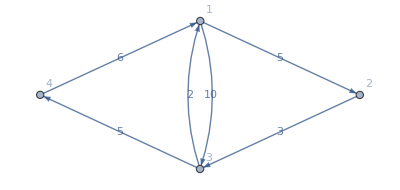

```mathematica
g1 =WeightedAdjacencyGraph[S,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]
```

{1,2,3}

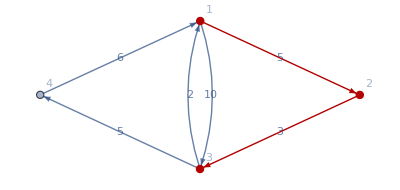

8.

```mathematica
sp =FindShortestPath[g1,1,3]
HighlightGraph[g1,PathGraph[sp,DirectedEdges->True],EdgeLabels->"EdgeWeight"]
GraphDistance[g1,1,3]
```

```mathematica
s= SparseArray[{
{1,2}->5,{1,3}->10,{1,6}->10,
{2,3}->3,{2,5}->6,
{3,4}->2,{3,5}->3,{3,6}->4,
{4,5}->2,{4,6}->5
},{6,6},Infinity];
S=Normal[s];
S//MatrixForm
```

(∞ | 5 | 10 | ∞ | ∞ | 10
∞ | ∞ | 3 | ∞ | 6 | ∞
∞ | ∞ | ∞ | 2 | 3 | 4
∞ | ∞ | ∞ | ∞ | 2 | 5
∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞)

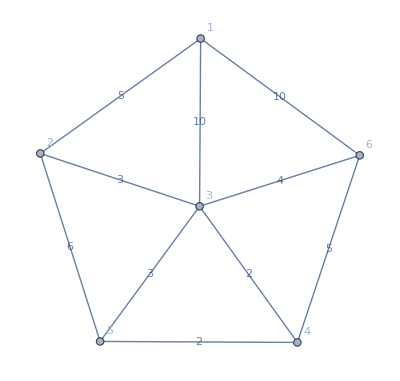

```mathematica
gs =WeightedAdjacencyGraph[S,DirectedEdges->False,VertexLabels->"Name", EdgeLabels->"EdgeWeight"]
```

```mathematica
fst = FindSpanningTree[gs, EdgeLabels->"EdgeWeight",PlotTheme->"Web"]
```

-Graphics-

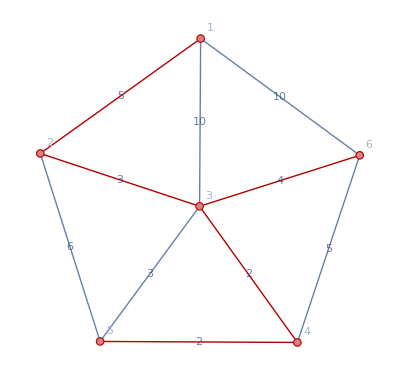

```mathematica
HighlightGraph[gs,fst,GraphHighlightStyle->"Thick"]
```

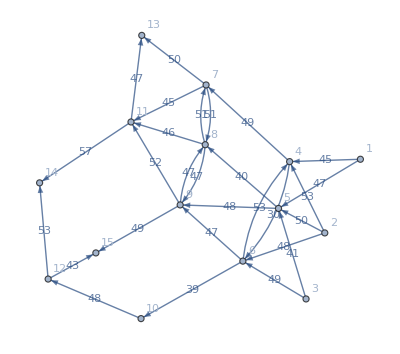

```mathematica
s=SparseArray[{
{1,4}->45,{1,5}->47,
{2,4}->53,{2,5}->50,{2,6}->48,
{3,5}->41,{3,6}->49,
{4,6}->30,{4,7}->49,
{5,8}->40,{5,9}->48,
{6,4}->53,{6,9}->47,{6,10}->39,
{7,13}->50,{7,11}->45,{7,8}->51,
{8,7}->51,{8,11}->46,{8,9}->47,
{9,8}->47,{9,11}->52,{9,15}->49,
{10,12}->48,
{11,13}->47,{11,14}->57,
{12,14}->53,{12,15}->43},
{15,15},Infinity];
S=Normal[s];
gs =WeightedAdjacencyGraph[S,VertexLabels->"Name",EdgeLabels->"EdgeWeight"]
```

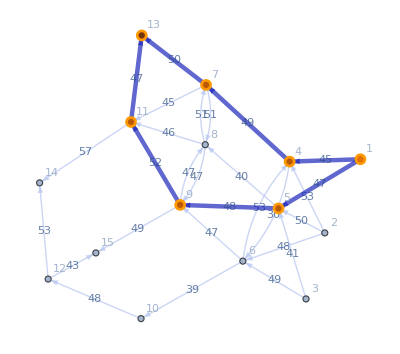

2

```mathematica
net =FindMaximumFlow[gs,1,13,"OptimumFlowData"];
net["FlowGraph"]
net["FlowValue"]
```

```mathematica
gst =WeightedAdjacencyGraph[S,VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
AnnotationKeys[gst]
ew = AnnotationValue[gst,EdgeWeight]
gstc = Graph[gst, EdgeCapacity->ew];
```

{EdgeShapeFunction,EdgeStyle,EdgeWeight,GraphHighlight,GraphHighlightStyle,GraphLayout,GraphStyle,VertexCoordinates,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

{45,47,53,50,48,41,49,30,49,40,48,53,47,39,51,45,50,51,47,46,47,52,49,48,47,57,53,43}

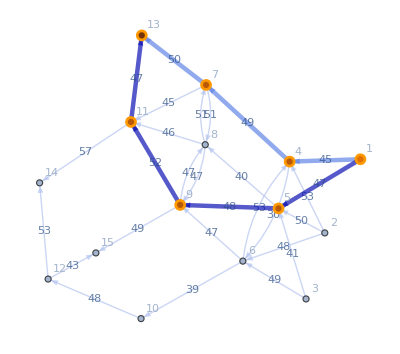

92

```mathematica
net =FindMaximumFlow[gstc,1,13,"OptimumFlowData"];
net["FlowGraph"]
net["FlowValue"]
```

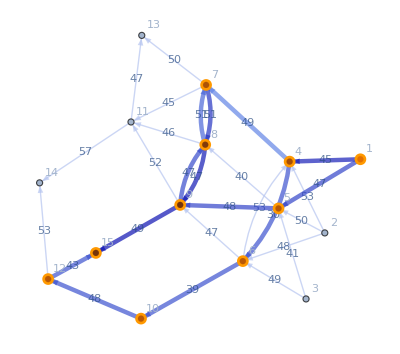

79

```mathematica
net =FindMaximumFlow[gstc,1,15,"OptimumFlowData"];
net["FlowGraph"]
net["FlowValue"]
```